```mathematica
Normalize[{2,2}]
```

{1/(√2),1/(√2)}

```mathematica
point[combo_,caps_]:=(#1+(combo-Floor[combo])(#2-#1))&@@@Transpose[caps[[Floor[combo]+1]]]
```

```mathematica
ccw90[p_]:={p[[2]],-p[[1]]}
cw90[p_]:={-p[[2]],p[[1]]}
```

```mathematica
capsule[{a_,b_},r_]:=(
 diff=b-a;
 u=Normalize[ccw90[diff]]*r;
d=Normalize[cw90[diff]]*r;
aUp=a+u;
aDown=a+d;
bUp=b+u;
bDown=b+d;
{Circle[a,r],Line[{aUp,bUp}],Line[{aDown,bDown}],Circle[b,r]}
)
capsuleSkeleton[{a_,b_},r_]:=(
 diff=b-a;
 u=Normalize[ccw90[diff]]*r;
d=Normalize[cw90[diff]]*r;
aUp=a+u;
aDown=a+d;
bUp=b+u;
bDown=b+d;
{Line[{a,b}]}
)
upside[a_,b_,r_]:=(
diff=b-a;
 u=Normalize[ccw90[diff]]*r;
d=Normalize[cw90[diff]]*r;
aUp=a+u;
aDown=a+d;
bUp=b+u;
bDown=b+d;
Line[{aUp,bUp}]
)
```

```mathematica
stroke17={6.875,6.375};
stroke18={7.21875,7.0};
stroke20={7.96875,7.9375};
stroke21={8.34375,8.1875};
```

enters at 17.48290604935480397
exits at 17.0.9075077419106311
exits at 20.7889052396611623

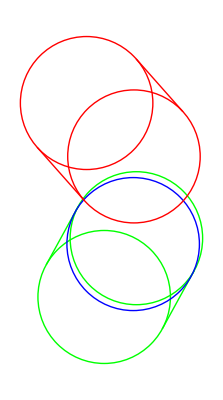

```mathematica
Graphics[{Green,capsule[stroke17,stroke18,Sqrt[0.5]],Blue,Circle[stroke17+.90(stroke18-stroke17),Sqrt[0.5]],Red,capsule[{6.6875,8.4375},{7.1875,7.875},Sqrt[0.5]]}]
```

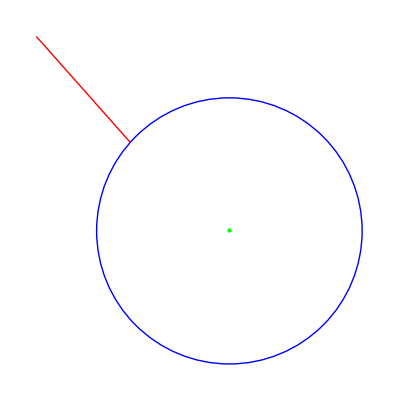

```mathematica
Graphics[{Green,Point[{7.1869557862817794,6.942192338694144}],Blue,Circle[stroke17+.90(stroke18-stroke17),Sqrt[0.5]],Red,upside[{6.6875,8.4375},{7.1875,7.875},Sqrt[0.5]]}]
```

{6.3138,8.10532}

{6.8138,7.54282}

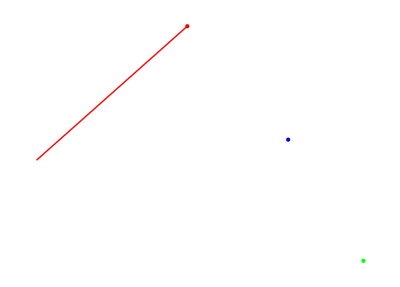

```mathematica
a={6.31379534065817,8.10531808058504}
b={6.81379534065817,7.54281808058504}
p={7.1869557862817794,6.942192338694144};
 diff=b-a;
norm=Normalize[ccw90[diff]];
Graphics[{Red,Point[a],Blue,Point[b],Red,Line[{a,a+norm}],Green,Point[p]}]
```

```mathematica
pDistance=Dot[p-a,norm]
```

0.12013

outside = true
topside:
0.9075077419106311
bcap:
0.48290604935480397

```mathematica
1.5-1.4986422195363014
```

0.00135778

```mathematica
0.0013577804636986102/5.0
```

0.000271556

```mathematica
param=0.00027155609273972204
```

0.000271556

```mathematica
0.004661554773294973*5
```

0.0233078

```mathematica
road=ToExpression[StringReplace["[(<10.0, 4.0> <10.0, 3.2928932188134525>), (<10.0, 3.2928932188134525> <10.0, 2.5>), (<10.0, 2.5> <9.937028689094806, 1.1111250243481652>), (<9.937028689094806, 1.1111250243481652> <9.755182680802518, -0.06279043882349643>), (<9.755182680802518, -0.06279043882349643> <9.465063861758075, -1.0326821938392188>), (<9.465063861758075, -1.0326821938392188> <9.077274118596431, -1.8094860450232353>), (<9.077274118596431, -1.8094860450232353> <8.602415337952529, -2.40413779669978>), (<8.602415337952529, -2.40413779669978> <8.051089406461307, -2.8275732531930875>), (<8.051089406461307, -2.8275732531930875> <7.433898210757714, -3.090728218827392>), (<7.433898210757714, -3.090728218827392> <6.761443637476695, -3.204538497926928>), (<6.761443637476695, -3.204538497926928> <6.044327573253193, -3.179939894815928>), (<6.044327573253193, -3.179939894815928> <5.293151904722154, -3.027868213818628>), (<5.293151904722154, -3.027868213818628> <4.51851851851852, -2.7592592592592604>), (<4.51851851851852, -2.7592592592592604> <3.7310293012772346, -2.385048835462058>), (<3.7310293012772346, -2.385048835462058> <2.9412861396332484, -1.9161727467512588>), (<2.9412861396332484, -1.9161727467512588> <2.159890920221497, -1.3635667974510932>), (<2.159890920221497, -1.3635667974510932> <1.3974455296769337, -0.7381667918857999>), (<1.3974455296769337, -0.7381667918857999> <0.6645518546344994, -0.05090853437960852>), (<0.6645518546344994, -0.05090853437960852> <-0.028188218270863097, 0.6872721707432445>), (<-0.028188218270863097, 0.6872721707432445> <-0.6701728024042063, 1.4654395191585272>), (<-0.6701728024042063, 1.4654395191585272> <-1.2508000111305904, 2.2726577065420046>), (<-1.2508000111305904, 2.2726577065420046> <-1.7594679578150645, 3.097990928569441>), (<-1.7594679578150645, 3.097990928569441> <-2.1855747558226897, 3.9305033809166035>), (<-2.1855747558226897, 3.9305033809166035> <-2.5185185185185177, 4.759259259259259>), (<-2.5185185185185177, 4.759259259259259> <-2.7476973592676064, 5.573322759273173>), (<-2.7476973592676064, 5.573322759273173> <-2.862509391435011, 6.361758076634111>), (<-2.862509391435011, 6.361758076634111> <-2.852352728385786, 7.113629407017836>), (<-2.852352728385786, 7.113629407017836> <-2.706625483484987, 7.81800094610012>), (<-2.706625483484987, 7.81800094610012> <-2.41472577009767, 8.463936889556726>), (<-2.41472577009767, 8.463936889556726> <-1.9660517015888903, 9.040501433063415>), (<-1.9660517015888903, 9.040501433063415> <-1.3500013913237048, 9.536758772295961>), (<-1.3500013913237048, 9.536758772295961> <-0.5559729526671684, 9.941773102930126>), (<-0.5559729526671684, 9.941773102930126> <0.42663550101566816, 10.244608620641678>), (<0.42663550101566816, 10.244608620641678> <1.6084258563597416, 10.434329521106381>), (<1.6084258563597416, 10.434329521106381> <3.0, 10.5>), (<3.0, 10.5> <3.7928932188134503, 10.5>), (<3.7928932188134503, 10.5> <4.5, 10.5>)]",{"> <"->"},{","<"|"("|"["->"{",">"|")"|"]"->"}"}]];
```

```mathematica
stroke={{{6.0,4.0}, {6.0,2.5}},{{6.0,2.5}, {6.0669097900390625,1.0655059814453125}},{{6.0669097900390625,1.0655059814453125}, {6.2598876953125,-0.1517333984375}},{{6.2598876953125,-0.1517333984375}, {6.5673065185546875,-1.1629791259765625}},{{6.5673065185546875,-1.1629791259765625}, {6.9775390625,-1.9794921875}},{{6.9775390625,-1.9794921875}, {7.4789581298828125,-2.6125335693359375}},{{7.4789581298828125,-2.6125335693359375}, {8.0599365234375,-3.0733642578125}},{{8.0599365234375,-3.0733642578125}, {8.708847045898438,-3.3732452392578125}},{{8.708847045898438,-3.3732452392578125}, {9.4140625,-3.5234375}},{{9.4140625,-3.5234375}, {10.163955688476562,-3.5352020263671875}},{{10.163955688476562,-3.5352020263671875}, {10.9468994140625,-3.4197998046875}},{{10.9468994140625,-3.4197998046875}, {11.751266479492188,-3.1884918212890625}},{{11.751266479492188,-3.1884918212890625}, {12.5654296875,-2.8525390625}},{{12.5654296875,-2.8525390625}, {13.377761840820312,-2.4232025146484375}},{{13.377761840820312,-2.4232025146484375}, {14.1766357421875,-1.9117431640625}},{{14.1766357421875,-1.9117431640625}, {14.950424194335938,-1.3294219970703125}},{{14.950424194335938,-1.3294219970703125}, {15.6875,-0.6875}},{{15.6875,-0.6875}, {16.376235961914062,0.0027618408203125}},{{16.376235961914062,0.0027618408203125}, {17.0050048828125,0.7301025390625}},{{17.0050048828125,0.7301025390625}, {17.562179565429688,1.4832611083984375}},{{17.562179565429688,1.4832611083984375}, {18.0361328125,2.2509765625}},{{18.0361328125,2.2509765625}, {18.415237426757812,3.0219879150390625}},{{18.415237426757812,3.0219879150390625}, {18.6878662109375,3.7850341796875}},{{18.6878662109375,3.7850341796875}, {18.842391967773438,4.5288543701171875}},{{18.842391967773438,4.5288543701171875}, {18.8671875,5.2421875}},{{18.8671875,5.2421875}, {18.750625610351562,5.9137725830078125}},{{18.750625610351562,5.9137725830078125}, {18.4810791015625,6.5323486328125}},{{18.4810791015625,6.5323486328125}, {18.046920776367188,7.0866546630859375}},{{18.046920776367188,7.0866546630859375}, {17.4365234375,7.5654296875}},{{17.4365234375,7.5654296875}, {16.638259887695312,7.9574127197265625}},{{16.638259887695312,7.9574127197265625}, {15.6405029296875,8.2513427734375}},{{15.6405029296875,8.2513427734375}, {14.431625366210938,8.435958862304688}},{{14.431625366210938,8.435958862304688}, {13.0,8.5}},{{13.0,8.5}, {11.5,8.5}}};
```

```mathematica
splitv={7.162395470248074,-3.1366789847251177};
```

```mathematica
combo=9.403748820065172;
(#1+(combo-Floor[combo])(#2-#1))&@@@Transpose[pre[[Floor[combo]+1]]]
```

{7.1624,-3.13668}

```mathematica
point[combo_,caps_]:=(#1+(combo-Floor[combo])(#2-#1))&@@@Transpose[caps[[Floor[combo]+1]]]
```

```mathematica
point[9.403748820065172,road]
```

{7.1624,-3.13668}

### what’s happening currently:

```mathematica
roadCombo=9.403748820065172;
```

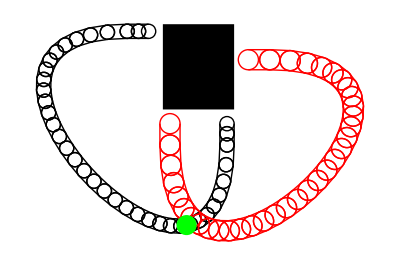

```mathematica
Graphics[{Rectangle[{5.5,5},{5.5+5,5+6}],capsule[#,0.5]&/@road,Red,capsule[#,0.7071067811865476]&/@stroke,Green,Disk[splitv,0.7071067811865476]}]
```

```mathematica
strokeAB={{6.960962001975423,-1.9464977636305323},{6.9748764916731325,-1.974192696054343}}
```

{{6.96096,-1.9465},{6.97488,-1.97419}}

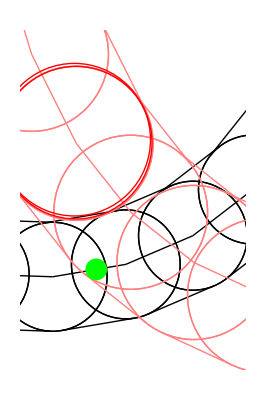

```mathematica
Graphics[{Rectangle[{5.5,5},{5.5+5,5+6}],capsule[#,0.5]&/@road,capsuleSkeleton[#,0.5]&/@road,Pink,capsule[#,0.7071067811865476]&/@stroke,capsuleSkeleton[#,0.7071067811865476]&/@stroke,Green,Disk[splitv,0.1],Red,capsule[strokeAB,0.7]},PlotRange->{{6.5,8.5},{-4,-1}}]
```

```mathematica
roadCombo=8.31808
strokeCombo=6.64775
```

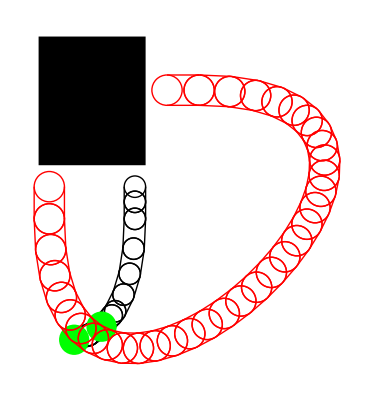

```mathematica
Graphics[{Rectangle[{5.5,5},{5.5+5,5+6}],capsule[#,0.5]&/@r0,capsule[#,0.5]&/@r1,Green,Disk[v4,0.7071067811865476],Disk[v5,0.7071067811865476],Red,capsule[#,0.7071067811865476]&/@s}]
```